Definitions

## Labels

### Labels for nodes

```mathematica
Options[op]={FontSize->12,FontWeight-> Bold,Background->White,FontFamily->"Arial"}
```

{FontSize→12,FontWeight→Bold,Background→-Graphics-,FontFamily→Arial}

```mathematica
op[x_,loc_]:=Text[Style[x,Options[op]],loc]
```

```mathematica
op["FFa",{1,2}]
```

Text[FFa,{1,2}]

```mathematica
op[Style["FFa",Green,16],{1,2}]
```

Text[FFa,{1,2}]

```mathematica
op["FFa",{1,2},FontSize->16]
```

op[FFa,{1,2},FontSize→16]

### Labels for arrows

```mathematica
Options[lab]={FontSize->12,FontWeight-> Bold,Background->White,FontFamily->"Arial"}
```

{FontSize→12,FontWeight→Bold,Background→-Graphics-,FontFamily→Arial}

```mathematica
lab[n_,p1_,p2_]:=Text[Style[Framed[n,FrameMargins->Tiny, FrameStyle->White,Background->White],Options[lab]],.5(p1+p2)]
```

```mathematica
lab["24F",{1,2},{3,5}]
```

Text[24F,{2.,3.5}]

## Diagram builder

To do : Figure out how to control arrowhead size.

```mathematica
Options[catdi]={ImageSize->130}
```

{ImageSize→130}

```mathematica
Options[cat3di]={ImageSize->130,Viewpoint->{0,-2,2}}
```

{ImageSize→130,Viewpoint→{0,-2,2}}

```mathematica
here=bol=beg={1,9}
```

{1,9}

```mathematica
ls={
ob["Fa"],nx;,
ob["FFa"],nx;,nl;,
ob["a"],nx;,
ob["Fa"],nl;}
```

{ob[Fa],Null,ob[FFa],Null,Null,ob[a],Null,ob[Fa],Null}

```mathematica
Join[{Arrowheads[Medium]},ls]
```

{Arrowheads[Medium],ob[Fa],Null,ob[FFa],Null,Null,ob[a],Null,ob[Fa],Null}

```mathematica
catdi[list_,size_]:=Graphics[Join[{Arrowheads[Medium]},list],ImageSize->size]
```

```mathematica
catdi[list_]:=Graphics[Join[{Arrowheads[Medium]},list],ImageSize->150]
```

```mathematica
cat3di[list_,size_,vp_]:=Graphics3D[list,ImageSize->size,ViewPoint->vp,Boxed->False]
```

```mathematica
cat3di[list_]:=Graphics3D[list,ImageSize->250,Viewpoint->{0,-2,2}]
```

## Grid nodes 1

This batch of nodes mimics xypic.  Below in grid notes 2 I introduce mnemonics.

```mathematica
tof[p_,h_,v_]:={p[[1]]+h,p[[2]]+v}
```

```mathematica
tol[p_]:=tof[p,-1,0]
```

```mathematica
tol[{2,5}]
```

{1,5}

```mathematica
tor[p_]:=tof[p,1,0]
```

```mathematica
tou[p_]:=tof[p,0,1]
```

```mathematica
tod[p_]:=tof[p,0,-1]
```

```mathematica
tord[p_]:=tof[p,1,-1]
```

```mathematica
told[p_]:=tof[p,-1,-1]
```

```mathematica
nx:=(here=tor[here];Null)
```

```mathematica
nl:=(bol=tod[bol];here=bol;Null)
```

```mathematica
ob[name_]:=op[name,here]
```

```mathematica
arl:=Arrow[{here,tol[here]},.1]
```

```mathematica
arr:=Arrow[{here,tor[here]},.1]
```

```mathematica
aru:=Arrow[{here,tou[here]},.1]
```

```mathematica
ard:=Arrow[{here,tod[here]},.1]
```

```mathematica
arld:=Arrow[{here,told[here]},.1]
```

```mathematica
arrd:=Arrow[{here,tord[here]},.1]
```

```mathematica
arrur:=Arrow[{here,tof[here,1,1]},.1]
```

```mathematica
lbl[n_]:=lab[n,here,tol[here]]
```

```mathematica
lbr[n_]:=lab[n,here,tor[here]]
```

```mathematica
lbu[n_]:=lab[n,here,tou[here]]
```

```mathematica
lbd[n_]:=lab[n,here,tod[here]]
```

```mathematica
lbld[n_]:=lab[n,here,told[here]]
```

```mathematica
lbrd[n_]:=lab[n,here,tord[here]]
```

```mathematica
lbur[n__]:=lab[n,here,tof[here,1,1]]
```

```mathematica
larl[n_]:=(arl;lbl[n])
```

```mathematica
larr[n_]:=(arr;lbr[n])
```

```mathematica
laru:=Arrow[{here,tou[here]},.1]
```

```mathematica
lard:=Arrow[{here,tod[here]},.1]
```

```mathematica
larld:=Arrow[{here,told[here]},.1]
```

```mathematica
larrd:=Arrow[{here,tord[here]},.1]
```

```mathematica
larrur:=Arrow[{here,tof[here,1,1]},.1]
```

```mathematica
ar2:=Subscript[ar,2]
```

```mathematica
ar2
```

ar_2

#### Center of a triangle

```mathematica
ctr[p1_,p2_,p3_]:=(1/3)(p1+p2+p3)
```

```mathematica
ctr[{0,0},{4,0},{2,Sqrt[3]/2}]
```

{2,1/(2 √3)}

### Example diagrams

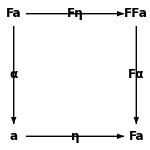

```mathematica
catdi[{
ob["Fa"],arr,lbr[Fη],ard,lbd[α],nx,
ob["FFa"],ard,lbd[Fα],nl,
ob["a"],arr,lbr[η],nx,
ob["Fa"],nl},150]
```

```mathematica
catdi[{
ob["Fa"],arr,lbr[Fη],ard,lbd[α],nx,
ob["FFa"],ard,lbd[Fα],nl,
ob["a"],arr,lbr[η],nx,
ob["Fa"],nl},100]
```

-Graphics-

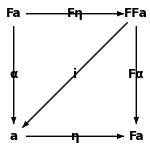

```mathematica
catdi[{
ob["Fa"],arr,lbr[Fη],ard,lbd[α],nx,
ob["FFa"],ard,lbd[Fα],arld,lbld[i],nl,
ob["a"],arr,lbr[η],nx,
ob["Fa"],nl}]
```

Diagrams for the GBLS Proof post

A diagram being described is in green.  The description is in black.  Cones (later) will be blue and fillin arrows (fias) will be red.

## Definitions

```mathematica
grn=RGBColor[0,.45,0]
```

-Graphics-

```mathematica
ar[p_,q_]:=Arrow[{p,q},{.1,.1}]
```

### Grid 2 : Introduce mnemonics

```mathematica
n11={1,1};n10={1,0};n01={0,1};n00={0,0};
```

```mathematica
ctr[n01,n11,n00]
```

{1/3,2/3}

## Examples

### Diagram 8.9 in GBLS

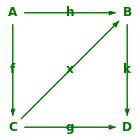

```mathematica
catdi[{grn,
ob["A"],arr,lbr[h],ard,lbd[f],nx,
ob["B"],ard,lbd[k],nl,
ob["C"],arr,lbr[g],arrur,lbur[x],nx,
ob["D"],nl},140]
```

#### Put in names for the two triangles

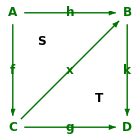

```mathematica
catdi[{grn,op["A",n01],ar[n01,n11],lab["h",n01,n11],
ar[n01,n00],lab["f",n01,n00],Black,
lab["S",n01,.5(n01+n10)],
lab["T",.5(n01+n10),n10],grn,
op["B",n11],ar[n11,n10],lab["k",n11,n10],
op["C",n00],ar[n00,n10],lab["g",n00,n10],
ar[n00,n11],lab["x",n00,n11],
op["D",n10]
},
140]
```

### Loops

Put a loop inside to indicate the triangle is commutative

```mathematica
commutative=Show[
{ParametricPlot[{Cos[θ],Sin[θ]},{θ,0.6,2 Pi-0.6},PlotRange->{{-1.2,1.4},{-1.3,1.3}},PlotStyle->grn,Axes->False],Graphics[{grn,Thickness[.04],Line[{{.3,.55},{.83,.57},{.76,1.1}}]}]},ImageSize->18]
```

-Graphics-

### Upper triangle

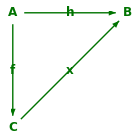

```mathematica
catdi[{grn,op["A",n01],ar[n01,n11],lab["h",n01,n11],
ar[n01,n00],lab["f",n01,n00],
op["B",n11],op["C",n00],
ar[n00,n11],lab["x",n00,n11]
},
140]
```

```mathematica
smallcommtri=catdi[{grn,op["A",n01],ar[n01,n11],lab["h",n01,n11],
ar[n01,n00],lab["f",n01,n00],
op["B",n11],op["C",n00],lab[commutative,n01,.5(n01+n10)],
ar[n00,n11],lab["x",n00,n11]
},
90]
```

-Graphics-

#### Hypothesis of the theorem

The two triangles commute

```mathematica
catdi[{grn,op["A",n01],ar[n01,n11],lab["h",n01,n11],
ar[n01,n00],lab["f",n01,n00],
lab[commutative,n01,.5(n01+n10)],
lab[commutative,.5(n01+n10),n10],
op["B",n11],ar[n11,n10],lab["k",n11,n10],
op["C",n00],ar[n00,n10],lab["g",n00,n10],
ar[n00,n11],lab["x",n00,n11],
op["D",n10]}]
```

-Graphics-

```mathematica
smallsquarecc=catdi[{grn,op["A",n01],ar[n01,n11],lab["h",n01,n11],
ar[n01,n00],lab["f",n01,n00],
lab[commutative,n01,.5(n01+n10)],
lab[commutative,.5(n01+n10),n10],
op["B",n11],ar[n11,n10],lab["k",n11,n10],
op["C",n00],ar[n00,n10],lab["g",n00,n10],
ar[n00,n11],lab["x",n00,n11],
op["D",n10]},80]
```

-Graphics-

Formal descriptions

## Formal description of the bare upper triangle

(The “formal description” is the form (as in GBLS) that specifies the bar upper triangle. "Bare" means the triangle is not assumed commutative.)

### Make a triangular lattice of nodes

```mathematica
Solve[Sqrt[4+a^2]==4,a]
```

{{a→-2 √3},{a→2 √3}}

Note that the arrowhead size is automatically scaled:

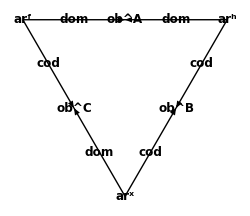

```mathematica
catdi[Module[{ts=2Sqrt[3],sb={Scaled[.001],Scaled[.0013]}},
{Arrowheads[.035],(*Mathematica automatically scales arrhowhead size*)
op["ob"^"C",{0,0}],
op["ob"^"A",{2,ts}],
op["ob"^"B",{4,0}],
op["ar"^"h",{6,ts}],
Arrow[{{6,ts},{2,ts}},sb],lab["dom",{6,ts},{2,ts}],
Arrow[{{6,ts},{4,0}},sb],lab["cod",{6,ts},{4,0}],
op["ar"^"f",{-2,ts}],
Arrow[{{-2,ts},{2,ts}},sb],lab["dom",{-2,ts},{2,ts}],
Arrow[{{-2,ts},{0,0}},sb],lab["cod",{-2,ts},{0,0}],
op["ar"^"x",{2,-ts}],
Arrow[{{2,-ts},{0,0}},sb],lab["dom",{2,-ts},{0,0}],
Arrow[{{2,-ts},{4,0}},sb],lab["cod",{2,-ts},{4,0}],
}
],250]
```

### Now do the same description using mnemonics for this specific diagram

The mnemonics are defined using nested modules.

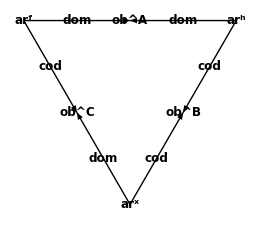

```mathematica
catdi[
Module[{ts=2Sqrt[3],sb={Scaled[.001],Scaled[.0012]}},
Module[{obAloc={2,ts},obBloc={4,0},obCloc={0,0},arfloc={-2,ts},arhloc={6,ts},arxloc={2,-ts}},
{
op["ob"^"C",obCloc],op["ob"^"A",obAloc],op["ob"^"B",obBloc],
op["ar"^"h",arhloc],Arrow[{arhloc,obAloc},sb],lab["dom",arhloc,obAloc],
Arrow[{arhloc,obBloc},sb],lab["cod",arhloc,obBloc],
op["ar"^"f",arfloc],Arrow[{arfloc,obAloc},sb],lab["dom",arfloc,obAloc],
Arrow[{arfloc,obCloc},sb],lab["cod",arfloc,obCloc],
op["ar"^"x",{2,-ts}],Arrow[{arxloc,obCloc},sb],lab["dom",arxloc,obCloc],
Arrow[{arxloc,obBloc},sb],lab["cod",arxloc,obBloc]
}]],260]
```

## The object ar_2 of composable arrows

#### ar_2 is this pullback:

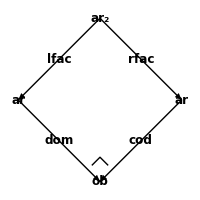

```mathematica
catdi[
Module[{sb={Scaled[.0004],Scaled[.0004]}},
Module[{toploc={1,1},lfacloc={0,0},rfacloc={2,0},baseloc={1,-1}},
{
op[ar2,toploc],op["ar",lfacloc],op["ar",rfacloc],op["ob",baseloc],
Arrow[{toploc,lfacloc},sb],lab["lfac",toploc,lfacloc],
Arrow[{toploc,rfacloc},sb],lab["rfac",toploc,rfacloc],
Arrow[{lfacloc,baseloc},sb],lab["dom",lfacloc,baseloc],
Arrow[{rfacloc,baseloc},sb],lab["cod",rfacloc,baseloc],
Line[{{.9,-.8},{1,-.7},{1.1,-.8}}]
}
]
],200]
```

### Blue cone form

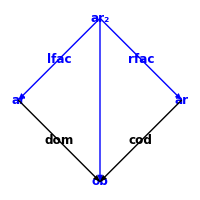

```mathematica
catdi[
Module[{sb={Scaled[.0004],Scaled[.0004]}},
Module[{toploc={1,1},lfacloc={0,0},rfacloc={2,0},baseloc={1,-1}},
{Blue,
op[ar2,toploc],op["ar",lfacloc],op["ar",rfacloc],op["ob",baseloc],
Arrow[{toploc,lfacloc},sb],lab["lfac",toploc,lfacloc],
Arrow[{toploc,rfacloc},sb],lab["rfac",toploc,rfacloc],
Arrow[{toploc,baseloc},sb],
Black,
Arrow[{lfacloc,baseloc},sb],lab["dom",lfacloc,baseloc],
Arrow[{rfacloc,baseloc},sb],lab["cod",rfacloc,baseloc]
}
]
],200]
```

## The commutative upper triangle

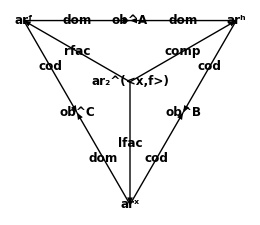

```mathematica
catdi[
Module[{ts=2Sqrt[3],sb={Scaled[.001],Scaled[.0012]}},
Module[{obAloc={2,ts},obBloc={4,0},obCloc={0,0},arfloc={-2,ts},arhloc={6,ts},arxloc={2,-ts},ctroid=ctr[{2,ts},{4,0},{0,0}]},
{
op["ob"^"C",obCloc],op["ob"^"A",obAloc],op["ob"^"B",obBloc],
op["ar"^"h",arhloc],Arrow[{arhloc,obAloc},sb],lab["dom",arhloc,obAloc],
Arrow[{arhloc,obBloc},sb],lab["cod",arhloc,obBloc],
op["ar"^"f",arfloc],Arrow[{arfloc,obAloc},sb],lab["dom",arfloc,obAloc],
Arrow[{arfloc,obCloc},sb],lab["cod",arfloc,obCloc],
op["ar"^"x",{2,-ts}],Arrow[{arxloc,obCloc},sb],lab["dom",arxloc,obCloc],
Arrow[{arxloc,obBloc},sb],lab["cod",arxloc,obBloc],op[ar2^"<x,f>",ctroid],
Arrow[{ctroid,arxloc},sb],lab["lfac",ctroid,arxloc],
Arrow[{ctroid,arfloc},sb],lab["rfac",ctroid,arfloc],Arrow[{ctroid,arhloc},{Scaled[.0017],Scaled[.0012]}],lab["comp",ctroid,arhloc]}]],260]
```

```mathematica
Remove[ctroid]
```

```mathematica
ctroid=ctr[{2,ts,2},{4,0,2},{0,0,2}]
```

### Blue cone form

```mathematica
Manipulate[
cat3di[
Module[{ts=2Sqrt[3],sb={Scaled[.0008],Scaled[.001]}},
Module[{obAloc={2,ts,0},obBloc={4,0,0},obCloc={0,0,0},arfloc={-2,ts,0},arhloc={6,ts,0},arxloc={2,-ts,0},ctroid=ctr[{2,ts,0},{4,0,0},{0,0,0}],limloc=ctr[{2,ts,h},{4,0,h},{0,0,h}]},
{Arrowheads[{.025}],
op["ob"^"C",obCloc],op["ob"^"A",obAloc],op["ob"^"B",obBloc],
op["ar"^"h",arhloc],Arrow[{arhloc,obAloc},sb],lab["dom",arhloc,obAloc],
Arrow[{arhloc,obBloc},sb],lab["cod",arhloc,obBloc],
op["ar"^"f",arfloc],Arrow[{arfloc,obAloc},sb],lab["dom",arfloc,obAloc],
Arrow[{arfloc,obCloc},sb],lab["cod",arfloc,obCloc],
op["ar"^"x",arxloc],Arrow[{arxloc,obCloc},sb],lab["dom",arxloc,obCloc],
Arrow[{arxloc,obBloc},sb],lab["cod",arxloc,obBloc],op[ar2^"<x,f>",ctroid],
Arrow[{ctroid,arxloc},sb],lab["lfac",ctroid,arxloc],
Arrow[{ctroid,arfloc},sb],lab["rfac",ctroid,arfloc+{m,n,p}],Arrow[{ctroid,arhloc},sb],lab["comp",ctroid,arhloc],Blue,
grn,op[Framed[smallcommtri],limloc+{0,0,.8}],Blue,Arrow[{limloc,ctroid},sb],Arrow[{limloc,obAloc},sb],Arrow[{limloc,obBloc},sb],Arrow[{limloc,obCloc},sb],Arrow[{limloc,arfloc},sb],Arrow[{limloc,arhloc},sb],Arrow[{limloc,arxloc},sb],
}
]
],600,{t,-2,v}],{{h,4.41},0,5},{{t,.41},-2,6},{{v,1.74},0,6},{{m,-.47},-1,1},{{n,.29},-1,1},{{p,0},-1,1}]
```

```mathematica
|
```

## This is diagram 6.4 in GBLS

#### This is the formal description of the bare diagram 8.9 (no commutativity)

```mathematica
cat3di[
Module[{sb={Scaled[.0003],Scaled[.0004]},obAloc={0,2,0},obBloc={2,2,0},obCloc={0,0,0},obDloc={2,0,0},arfloc={-1,1,0},arhloc={1,3,0},arxloc={1,1,0},argloc={1,-1,0},arkloc={3,1,0}
},
{Arrowheads[.015],
op["ob"^"C",obCloc],op["ob"^"B",obBloc],op["ob"^"A",obAloc],op["ob"^"D",obDloc],
op["ar"^"h",arhloc],Arrow[{arhloc,obAloc},sb],lab["dom",arhloc,obAloc],
Arrow[{arhloc,obBloc},sb],lab["cod",arhloc,obBloc],
op["ar"^"f",arfloc],Arrow[{arfloc,obAloc},sb],lab["dom",arfloc,obAloc],
Arrow[{arfloc,obCloc},sb],lab["cod",arfloc,obCloc],op["ar"^"k",arkloc],Arrow[{arkloc,obBloc},sb],lab["dom",arkloc,obBloc],
Arrow[{arkloc,obDloc},sb],lab["cod",arkloc,obDloc],op["ar"^"g",argloc],Arrow[{argloc,obCloc},sb],lab["dom",argloc,obCloc],
Arrow[{argloc,obDloc},sb],lab["cod",argloc,obDloc],
op["ar"^"x",{1,1,0}],Arrow[{arxloc,obCloc},sb],lab["dom",arxloc,obCloc],
Arrow[{arxloc,obBloc},sb],lab["cod",arxloc,obBloc]
}
],600, {0,-2,2}
]
```

-Graphics3D-

## Diagram 8.10

This form inserts the composable pairs but does not require anything to commute.

```mathematica
Manipulate[
cat3di[
Module[{sb={Scaled[.0003],Scaled[.0004]},obAloc={0,2,0},obBloc={2,2,0},obCloc={0,0,0},obDloc={2,0,0},arfloc={-1,1,0},arhloc={1,3,0},arxloc={1,1,0},argloc={1,-1,0},arkloc={3,1,0},arxfloc={-.5,.5,k},arkxloc={1.5,.5,k}
},
{Arrowheads[.02],
op["ob"^"C",obCloc],op["ob"^"B",obBloc],op["ob"^"A",obAloc],op["ob"^"D",obDloc],
op["ar"^"h",arhloc],Arrow[{arhloc,obAloc},sb],lab["dom",arhloc,obAloc],
Arrow[{arhloc,obBloc},sb],lab["cod",arhloc,obBloc],
op["ar"^"f",arfloc],Arrow[{arfloc,obAloc},sb],lab["dom",arfloc,obAloc],
Arrow[{arfloc,obCloc},sb],lab["cod",arfloc,obCloc],op["ar"^"k",arkloc],Arrow[{arkloc,obBloc},sb],lab["dom",arkloc,obBloc],
Arrow[{arkloc,obDloc},sb],lab["cod",arkloc,obDloc],op["ar"^"g",argloc],Arrow[{argloc,obCloc},sb],lab["dom",argloc,obCloc],
Arrow[{argloc,obDloc},sb],lab["cod",argloc,obDloc],
op["ar"^"x",{1,1,0}],Arrow[{arxloc,obCloc},sb],lab["dom",arxloc,obCloc],
Arrow[{arxloc,obBloc},sb],lab["cod",arxloc,obBloc],op[ar2^"<x,f>",arxfloc],op[ar2^"<k,x>",arkxloc],
Arrow[{arxfloc,arxloc},sb],lab["lfac",arxfloc,arxloc],Arrow[{arxfloc,arfloc},sb],lab["rfac",arxfloc,arfloc],Arrow[{arkxloc,arkloc},sb],lab["lfac",arkxloc,arkloc],Arrow[{arkxloc,arxloc},sb],lab["rfac",arkxloc,arxloc]
}
],600,{r,s,t}
],{{k,1.75},-2,3},{{r,0.14},-4,4},{{s,-2.35},-4,4},{{t,1.2},-4,4}]
```

```mathematica
{{h,0},-1,3},{{k,1.75},-2,3},{{m,3},-1,3},{{s,.585},-1,1},{{t,0},-1,1},{{{{u,0.14},-5,5},, {{v,-2.35},-5,5},, {{w,1.2},-5,5}}}]
```

## Diagram 8.11 (makes the triangles commute)

```mathematica
ar2^"<g,f>"
```

ar_2^(<g,f>)

```mathematica
ar2^"<k,h>"
```

ar_2^(<k,h>)

Diagram 8.11 in GBLS contains two extra nodes, ar_2^(<g,f>) and ar_2^(<k,h>), that are not shown in the diagram below.  Putting them in or leaving them out have no effect on the limit of the diagram because the pullback property causes the existence of a fill-in arrow (fia) from the limit to each of the nodes that causes the resulting cone to still be commutative and does not affect the limit. (This is an example of Lemma 5.4.5 of GBLS for the “adjoining a limit” case.)

```mathematica
Manipulate[
cat3di[
Module[{sb={Scaled[.0002],Scaled[.0003]},obAloc={0,2,0},obBloc={2,2,0},obCloc={0,0,0},obDloc={2,0,0},arfloc={-1,1,h},arhloc={1,3,h},arxloc={1,1,h},argloc={1,-1,h},arkloc={3,1,h},arxfloc={-.5,.5,k},arkxloc={1.5,.5,m}
},
{Arrowheads[.015],
op["ob"^"C",obCloc],op["ob"^"B",obBloc],op["ob"^"A",obAloc],op["ob"^"D",obDloc],
op["ar"^"h",arhloc],Arrow[{arhloc,obAloc},sb],lab["dom",arhloc+{s,.2s,+.45s},obAloc],
Arrow[{arhloc,obBloc},sb],lab["cod",arhloc,obBloc],
op["ar"^"f",arfloc],Arrow[{arfloc,obAloc},sb],lab["dom",arfloc,obAloc],
Arrow[{arfloc,obCloc},sb],lab["cod",arfloc,obCloc],op["ar"^"k",arkloc],Arrow[{arkloc,obBloc},sb],lab["dom",arkloc,obBloc],
Arrow[{arkloc,obDloc},sb],lab["cod",arkloc,obDloc],op["ar"^"g",argloc],Arrow[{argloc,obCloc},sb],lab["dom",argloc,obCloc],
Arrow[{argloc,obDloc},sb],lab["cod",argloc,obDloc],
op["ar"^"x",{1,1,h}],Arrow[{arxloc,obCloc},sb],lab["dom",arxloc+{t,.05,+.6t},obCloc],
Arrow[{arxloc,obBloc},sb],lab["cod",arxloc,obBloc],op[ar2^"<x,f>",arxfloc],op[ar2^"<k,x>",arkxloc],
Arrow[{arxfloc,arxloc},sb],lab["lfac",arxfloc,arxloc],Arrow[{arxfloc,arfloc},sb],lab["rfac",arxfloc,arfloc],Arrow[{arkxloc,arkloc},sb],lab["lfac",arkxloc,arkloc],Arrow[{arkxloc,arxloc},sb],lab["rfac",arkxloc+{-.1,0,0},arxloc],
Arrow[{arxfloc,arhloc},sb],lab[ "comp",arxfloc,arhloc],Arrow[{arkxloc,argloc},sb],lab["comp",arkxloc+{.1,0,0},argloc]
}
],650,{u,v,w}
],{{h,0},-1,3},{{k,2.63},-2,5},{{m,2.53},-1,5},{{s,-0.065},-1,1},{{t,0},-1,1},{{u,-0.12},-5,5},{{v,-3.72},-5,5},{{w,1.16},-5,5},ControlPlacement->Right]
```

```mathematica
{{{{u,0.14},-5,5},, {{v,-2.35},-5,5},, {{w,1.2},-5,5}}}
```

### Blue cone form

```mathematica
Manipulate[
cat3di[
Module[{sb={Scaled[.0002],Scaled[.0003]},obAloc={0,2,0},obBloc={2,2,0},obCloc={0,0,0},obDloc={2,0,0},arfloc={-1,1,h},arhloc={1,3,h},arxloc={1,1,h},argloc={1,-1,h},arkloc={3,1,h},arxfloc={-.5,.5,k},arkxloc={1.5,.5,m},limloc={.5,.5,z}
},
{Arrowheads[.015],
op["ob"^"C",obCloc],op["ob"^"B",obBloc],op["ob"^"A",obAloc],op["ob"^"D",obDloc],
op["ar"^"h",arhloc],Arrow[{arhloc,obAloc},sb],lab["dom",arhloc+{s,.2s,+.45s},obAloc],
Arrow[{arhloc,obBloc},sb],lab["cod",arhloc,obBloc],
op["ar"^"f",arfloc],Arrow[{arfloc,obAloc},sb],lab["dom",arfloc,obAloc],
Arrow[{arfloc,obCloc},sb],lab["cod",arfloc,obCloc],op["ar"^"k",arkloc],Arrow[{arkloc,obBloc},sb],lab["dom",arkloc,obBloc],
Arrow[{arkloc,obDloc},sb],lab["cod",arkloc,obDloc],op["ar"^"g",argloc],Arrow[{argloc,obCloc},sb],lab["dom",argloc,obCloc],
Arrow[{argloc,obDloc},sb],lab["cod",argloc,obDloc],
op["ar"^"x",{1,1,h}],Arrow[{arxloc,obCloc},sb],lab["dom",arxloc+{t,.05,+.6t},obCloc],
Arrow[{arxloc,obBloc},sb],lab["cod",arxloc,obBloc],op[ar2^"<x,f>",arxfloc],op[ar2^"<k,x>",arkxloc],
Arrow[{arxfloc,arxloc},sb],lab["lfac",arxfloc,arxloc],Arrow[{arxfloc,arfloc},sb],lab["rfac",arxfloc,arfloc],Arrow[{arkxloc,arkloc},sb],lab["lfac",arkxloc,arkloc],Arrow[{arkxloc,arxloc},sb],lab["rfac",arkxloc+{-.1,0,0},arxloc],
Arrow[{arxfloc,arhloc},sb],lab[ "comp",arxfloc,arhloc],Arrow[{arkxloc,argloc},sb],lab["comp",arkxloc+{.1,0,0},argloc],grn,op[Framed[smallsquarecc],limloc+{0,0,.08}],Blue,Arrow[{limloc,arxfloc},sb],Arrow[{limloc,arkxloc},sb]
}
],650,{u,v,w}
],{{h,0},-1,3},{{k,2.63},-2,5},{{m,2.53},-1,5},{{s,-0.065},-1,1},{{t,0},-1,1},{{u,-0.12},-5,5},{{v,-3.72},-5,5},{{w,1.16},-5,5},{{z,3.5},0,5},ControlPlacement->Right]
```